# Fisher matrix for multiple tracers: Model independent constraints on fσ8.

## Code by Renan Boschetti, Luca Amendola and Raul Abramo. April, 2020. This notebook produce relative marginalized errors for r = fσ_8(z_1)/fσ_8(z_2), which we call σ_r, per unit of phase-space volume. We derive σ_r in the case where it is drawn from the two-tracers Fisher matrix as well as in the case where it is drawn from the single-tracer Fisher matrix, with the single-tracer being the combination of the two individual tracers we used in the two-tracers Fisher matrix. This notebook reproduces figures 1 and 2 of the paper and the reader can explore the space of parameters in order to plot similar figures for another configurations. This notebook takes about 8 minutes to run in a modest laptop. The usage of this notebook is free. If you use it in a publication, please cite the paper.

## One tracer, two redshift bins:

```mathematica
Clear["Global`*"]
```

```mathematica
(*This is the single-tracer Fisher matrix (see, for instance, arXiv:astro-ph/9706198v3):*)
Fishsingle= (𝒫/(1.+𝒫))^2.;

𝒫 = P*Exp[-μ^2.*k^2.*σ^2.]*(1+β*μ^2.)^2.;

aux1 = ArrayFlatten[{{Fishsingle, {{0}}}}]/.{P-> P1bar, β->β1bar};
```

```mathematica
P2bar = q*(β1bar^2./β2bar^2.)*(P1bar/r^2.);

aux2 = ArrayFlatten[{{{{0}}, Fishsingle}}]/.{P->P2bar, β-> β2bar};

Fishsinglez1z2 = Join[aux1, aux2];

𝒫1bar = P1bar*Exp[-μ^2.*k^2.*σ^2.]*(1+β1bar*μ^2.)^2.;

𝒫2bar =P2bar*Exp[-μ^2.*k^2.*σ^2.]*(1+β2bar*μ^2.)^2.;

paroldsingle = {𝒫1bar, 𝒫2bar};

parnewsingle= {r, P1bar, β1bar,β2bar, σ};
```

```mathematica
(* Projecting ..*)
```

```mathematica
Fishsinglenew[q_,r_,P1bar_,β1bar_,β2bar_,σ_,k_]=
Table[Sum[(parnewsingle[[i]]/paroldsingle[[a]])*D[paroldsingle[[a]], parnewsingle[[i]]]*Fishsinglez1z2[[a,b]]*(parnewsingle[[j]]/paroldsingle[[b]])*D[paroldsingle[[b]], parnewsingle[[j]]], {a,1, Length[Fishsinglez1z2]}, {b,1, Length[Fishsinglez1z2]}], {i, 1, Length[parnewsingle]},{j,1,Length[parnewsingle]}]; // AbsoluteTiming
```

{0.017899,Null}

```mathematica
(* Averaging over μ and inverting:*)
covrsingle[q_,r_,P1bar_,β1bar_,β2bar_,σ_,k_]:= Inverse[(1./2.)*NIntegrate[Fishsinglenew[q,r,P1bar,β1bar,β2bar,σ,k], {μ,-1,1}, Method->{Automatic,"SymbolicProcessing"->0}]]; // AbsoluteTiming

sigmarsingle[q_,r_,P1bar_,β1bar_,β2bar_,σ_,k_]:= Sqrt[covrsingle[q,r,P1bar,β1bar,β2bar,σ,k][[1,1]]];
```

{0.000018,Null}

```mathematica
(*Testing ..*)
sigmarsingle[1.,1. ,20.,0.5,1.,4.,0.1] // AbsoluteTiming
```

{0.018186,10.5719}

## Two tracers, two redshift bins:

```mathematica
(* Initially we have the following degrees of freedom {r, P1bar1, P1bar2, P2bar1, P2bar2, β1bar1, β1bar2, β2bar1, β2bar2, σ1, σ2}. With these relations, we can reduce the degrees of freedom to {r, Pz1bar, β1bar1,β1bar2,β2bar1,β2bar2, σ1,σ2}:*)
```

```mathematica
Z1bar = (((1.+ q1bar*Exp[-0.5*μ^2.*k^2.*(σ2^2.-σ1^2.)]*(β1bar1/β1bar2))^2.)*(1.+q1bar))/((1.+Exp[-0.5*μ^2.*k^2.*(σ2^2.-σ1^2.)]*q1bar)^2.);

Z2bar =(((1.+ q2bar*Exp[-0.5*μ^2.*k^2.*(σ2^2.-σ1^2.)]*(β2bar1/β2bar2))^2.)*(1.+q2bar))/((1.+Exp[-0.5*μ^2.*k^2.*(σ2^2.-σ1^2.)]*q2bar)^2.);

Pz2bar = q1*(Z2bar/Z1bar)*(Pz1bar/r^2.)*(β1bar1^2./β2bar1^2.);

Y1bar = ((β1bar1/β1bar2)^2.)*q1bar;

Y2bar = ((β2bar1/β2bar2)^2.)*q2bar;

P1bar1 = Pz1bar/Z1bar;

P1bar2 = Pz1bar*Y1bar/Z1bar;

P2bar1 = Pz2bar/Z2bar;

P2bar2 = Pz2bar*Y2bar/Z2bar;

𝒫2t={𝒫2t1, 𝒫2t2};

(*The two-tracers Fisher matrix (equation (22) on the paper):*)
fish2t = (1./2.)*Table[KroneckerDelta[i,j]*𝒫2t[[i]]*Sum[𝒫2t[[k]],{k,1,2}]/(1.+Sum[𝒫2t[[k]],{k,1,2}])+𝒫2t[[i]]*𝒫2t[[j]]*(1-Sum[𝒫2t[[k]],{k,1,2}])/((1+Sum[𝒫2t[[k]],{k,1,2}])^2), {i, 1,2}, {j, 1,2}];

aux1 = ArrayFlatten[{ { fish2t, {{ 0,0 }, {0,0}}   } }]/.{𝒫2t1-> P1bar1*Exp[-μ^2.*k^2.*σ1^2.]*(1+β1bar1*μ^2.)^2., 𝒫2t2-> P1bar2*Exp[-μ^2.*k^2.*σ2^2.]*(1+β1bar2*μ^2.)^2.};

aux2 = ArrayFlatten[{ {  {{ 0,0 }, {0,0}}, fish2t   } }]/.{𝒫2t1-> P2bar1*Exp[-μ^2.*k^2.*σ1^2.]*(1+β2bar1*μ^2.)^2., 𝒫2t2->P2bar2*Exp[-μ^2.*k^2.*σ2^2.]*(1+β2bar2*μ^2.)^2.};
(*This is the Fisher matrix for two tracers and two redshift bins, which has as parameters {𝒫1bar1, 𝒫1bar2, 𝒫2bar1, 𝒫2bar2}*)
fish2tz1z2 = Join[aux1, aux2];
```

```mathematica
𝒫1bar1 = P1bar1*Exp[-μ^2.*k^2.*σ1^2.]*(1+β1bar1*μ^2.)^2.;

𝒫1bar2 = P1bar2*Exp[-μ^2.*k^2.*σ2^2.]*(1+β1bar2*μ^2.)^2.;

𝒫2bar1 = P2bar1*Exp[-μ^2.*k^2.*σ1^2.]*(1+β2bar1*μ^2.)^2.;

𝒫2bar2 = P2bar2*Exp[-μ^2.*k^2.*σ2^2.]*(1+β2bar2*μ^2.)^2.;

(* Initially we have the Fisher matrix for the set:*)
paroldz2t = {𝒫1bar1, 𝒫1bar2, 𝒫2bar1, 𝒫2bar2};

(* We would like to project this Fisher matrix into the set of independent variables:*)
parnewz2t = {r, Pz1bar, β1bar1,β1bar2,β2bar1,β2bar2, σ1,σ2};
(* Projecting ..*)
fish2tnew[r_,Pz1bar_,β1bar1_,β1bar2_, β2bar1_,β2bar2_, q1bar_,q2bar_,q1_, σ1_,σ2_,k_]=Table[Sum[(parnewz2t[[i]]/paroldz2t[[a]])*D[paroldz2t[[a]], parnewz2t[[i]]]*fish2tz1z2[[a,b]]*(parnewz2t[[j]]/paroldz2t[[b]])*D[paroldz2t[[b]], parnewz2t[[j]]], {a,1, Length[fish2tz1z2]}, {b,1, Length[fish2tz1z2]}], {i, 1, Length[parnewz2t]},{j,1,Length[parnewz2t]}]; // AbsoluteTiming
(* Averaging over μ and inverting:*)
cov2t[r_,Pz1bar_,β1bar1_,β1bar2_, β2bar1_,β2bar2_, q1bar_,q2bar_,q1_, σ1_,σ2_,k_] := Inverse[(1./2.)*NIntegrate[fish2tnew[r,Pz1bar,β1bar1,β1bar2, β2bar1,β2bar2, q1bar,q2bar,q1, σ1,σ2,k], {μ,-1,1}, Method->{Automatic,"SymbolicProcessing"->0}]];

sigmar2t[r_,Pz1bar_,β1bar1_,β1bar2_, β2bar1_,β2bar2_, q1bar_,q2bar_,q1_, σ1_,σ2_,k_] :=Sqrt[cov2t[r,Pz1bar,β1bar1,β1bar2, β2bar1,β2bar2, q1bar,q2bar,q1,σ1,σ2,k][[1,1]]];
```

{0.288007,Null}

```mathematica
(*Testing..*)
sigmar2t[0.5,10.,1.,0.5, 1.,0.5, 1.,1.,1., 2.,3.,0.1] // AbsoluteTiming
```

{0.575995,3.77369}

```mathematica
(*The combined redshift distortion parameter and velocity dispersion:*)
```

```mathematica
βfunzσ[qibar_,βibar1_, βibar2_,σ1_,σ2_,k_]:= (1.+Exp[-0.5*μ^2.*k^2.*(σ2^2.-σ1^2.)]*qibar)*βibar1*βibar2/(βibar2+qibar*Exp[-0.5*μ^2.*k^2.*(σ2^2.-σ1^2.)]*βibar1);

σfun[qibar_, k_,σ1_,σ2_]:=Sqrt[-(2./(μ^2.*k^2.))*Log[(Exp[-0.5*μ^2.*k^2.*σ1^2.]+qibar*Exp[-0.5*μ^2.*k^2.*σ2^2.])/(1.+qibar)]];
```

## Results

σ_r as a function of  P_(1^-):

```mathematica
(*Here you can choose some values of paramaters for plotting σr as function of P_(1^-):*)
β1bar1values = {0.25, 0.5};
q = 1;
r = 1;
β1bar1 = 0.5;
β1bar2 = 1.0;
β2bar1 = 0.5;
β2bar2 = 1.0;
σ1 = 4.;
σ2 = 2.;
q1 = 1.;
q1bar = 1.;
q2bar = 1.;
k = 0.1;
p = Table[10^p, {p, -1., 2., 0.05}];
```

```mathematica
σrPtable1t = Table[{p[[j]],sigmarsingle[q,r,p[[j]],βfunzσ[q1bar,β1bar1values[[i]],β1bar2,σ1, σ2, k],βfunzσ[q2bar,β1bar1values[[i]],β2bar2,σ1, σ2, k], σfun[q1bar, k,σ1,σ2], k]},{i,1, Length[β1bar1values]}, {j, 1, Length[p]}]; // AbsoluteTiming
```

{5.41817,Null}

```mathematica
σrPtable2t = Table[{p[[j]],sigmar2t[r,p[[j]],β1bar1values[[i]],β1bar2, β1bar1values[[i]],β2bar2, q1bar,q2bar,q1, σ1, σ2,k]},{i,1, Length[β1bar1values]}, {j, 1, Length[p]}]; // AbsoluteTiming
```

{65.6584,Null}

```mathematica
σrPtable1tinterp = Table[Interpolation[σrPtable1t [[i]],  InterpolationOrder -> 10], {i,1, Length[β1bar1values]}];
σrPtable2tinterp = Table[Interpolation[σrPtable2t [[i]],  InterpolationOrder -> 10], {i,1, Length[β1bar1values]}];
```

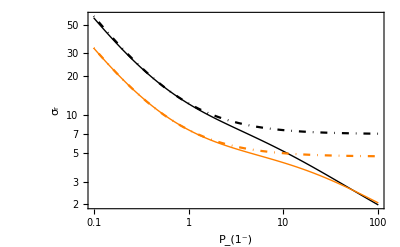

```mathematica
LogLogPlot[{σrPtable1tinterp [[1]][p],σrPtable2tinterp [[1]][p],σrPtable1tinterp [[2]][p],σrPtable2tinterp [[2]][p] },{p,.1,100},PlotStyle->{{Black,DotDashed},{Black,Thick}, {Orange,DotDashed},{Orange,Thick}},(*PlotRange->{1.9,20},*)Frame->True,FrameLabel->{"P_(1^-)","σ_r"},BaseStyle->{15,FontFamily->"Times"} ]
```

σ_r as a function of  β_(1^-1):

{28.4528,Null}

{341.921,Null}

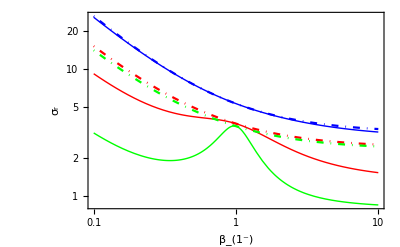

```mathematica
(*Here you can choose some values of paramaters for plotting σr as function of Subscript[β, 1^-1]:*)
P1barvalues = {1., 10., 100.};
q = 1;
r = 1;
β1bar1 = 0.5;
β1bar2 = 1.0;
β2bar1 = 0.5;
β2bar2 = 1.0;
σ1 = 4.;
σ2 = 2.;
q1 = 1.;
q1bar = 1.;
q2bar = 1.;
k = 0.1;
β1bar1table = Table[10^β1bar1, {β1bar1,-1., 1., 0.01}];
σrβtable1t = Table[{β1bar1table[[j]],sigmarsingle[q,r,P1barvalues[[i]],βfunzσ[q1bar,β1bar1table[[j]],β1bar2,σ1, σ2, k],βfunzσ[q2bar,β1bar1table[[j]],β2bar2,σ1, σ2, k], σfun[q1bar, k,σ1,σ2], k]},{i,1, Length[P1barvalues]}, {j, 1, Length[β1bar1table]}]; // AbsoluteTiming
σrβtable2t = Table[{β1bar1table[[j]],sigmar2t[r,P1barvalues[[i]],β1bar1table[[j]],β1bar2, β1bar1table[[j]],β2bar2, q1bar,q2bar,q1, σ1, σ2,k]},{i,1, Length[P1barvalues]}, {j, 1, Length[β1bar1table]}]; // AbsoluteTiming
σrβtable1tinterp = Table[Interpolation[σrβtable1t [[i]],  InterpolationOrder -> 10], {i,1, Length[P1barvalues]}];
σrβtable2tinterp = Table[Interpolation[σrβtable2t [[i]],  InterpolationOrder -> 10], {i,1, Length[P1barvalues]}];
LogLogPlot[{σrβtable1tinterp [[1]][β1bar1],σrβtable2tinterp [[1]][β1bar1],σrβtable1tinterp [[2]][β1bar1],σrβtable2tinterp [[2]][β1bar1],σrβtable1tinterp [[3]][β1bar1],σrβtable2tinterp [[3]][β1bar1]},{β1bar1,.1,10.},PlotStyle->{{Blue,DotDashed},{Blue,Thick}, {Red,DotDashed},{Red,Thick}, {Green,DotDashed},{Green,Thick}},(*PlotRange->{1.9,20},*)Frame->True,FrameLabel->{"β_(1^-)","σ_r"},BaseStyle->{15,FontFamily->"Times"} ]
```